```mathematica
Clear["Global`*"]
```

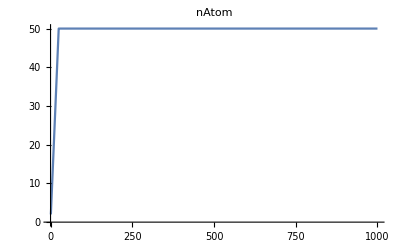

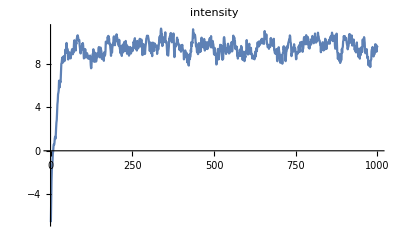

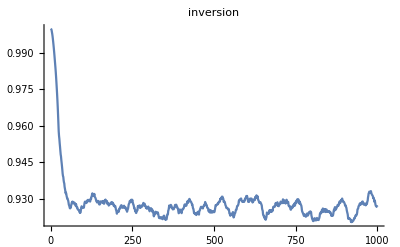

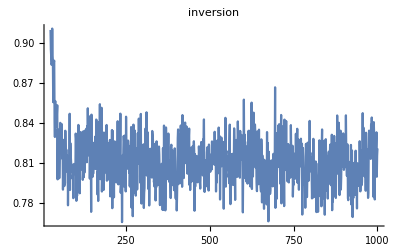

```mathematica
(*When doing one run*)
name ="tau0.5_dens100_g1.4_k20";
intensityy=Flatten[Import[NotebookDirectory[]<>name<>"/intensity.dat"]];
nAtomm=Flatten[Import[NotebookDirectory[]<>name<>"/nAtom.dat"]];
inversionnAve=Flatten[Import[NotebookDirectory[]<>name<>"/inversionAve.dat"]];
inversionnFinal=Flatten[Import[NotebookDirectory[]<>name<>"/inversionFinal.dat"]];
ListLinePlot[nAtomm,PlotRange->All,PlotLabel->nAtom]
ListLinePlot[intensityy,PlotRange->All,PlotLabel->intensity]
ListLinePlot[inversionnAve,PlotRange->All,PlotLabel->inversion]
ListLinePlot[inversionnFinal,PlotRange->All,PlotLabel->inversion]
```